Finite Friction Model, non-dimensionalize
what happens if μ is not infinite?
To increase separation by S in x, what minimum initial separation D in y is needed?

Set the horizontal boundary at y = D, particle 1 starts in contact with the boundary at (0,D), particle 2 starts at (0,0).  Initial separation is D.
We command a move of lengh d at angle θ  (d Sin[θ] = D).
particle 2 ends at (d Cos[θ],d Sin[θ] = D)
particle 1 ends at (d Cos[θ]- Friction,D)
Friction = d Min[Cos[θ],μSin[θ]]
We want the final x separation to be S
S = d Cos[θ] - d Max( Cos[θ] - μSin[θ],0)
There are two possible optimizations problems: we can minimize d or minimize d Sin θ. These give the same answer:
To minimize the commanded distance d, pick θ = ArcCot[μ]. We require μ>0.

That means to increase separation by S in x, we need initial separation D in y, where D = S/μ.

### The coefficient of friction depends on the objects that are causing friction. The value is usually between 0 and 1 but can be greater than 1. A value of 0 means there is no friction at all between the objects. This is only theoretically possible. All objects in the real world will have some friction when they touch each other. A value of 1 means the frictional force is equal to the normal force. Some people think that the coefficient of friction can never be more than 1, but this is not true. A coefficient of friction that is more than one just means that friction is stronger than the normal force. An object such as silicone rubber, for example, can have a coefficient of friction much greater than one. The coefficient of friction can also be changed by the mass and speed of the moving object.

```mathematica
mind=Plot3D[{1/Cos[θ],1/(μ Sin[θ])},{μ,0,10},{θ,0,π/2},AxesLabel->{"μ","θ","d/S"},MaxRecursion->8,PlotLabel->"Minimize commanded distance d",PlotLegends->"Expressions"];
Show[mind,divLind]
divLind =ParametricPlot3D[{Cot[θ],θ,1/(Cot[θ] Sin[θ])},{θ,0,π/2},PlotStyle->Red];
```

```mathematica
mindSin =Plot3D[{Tan[θ],1/μ},{μ,0.1,10},{θ,0,1.5},AxesLabel->{"μ","θ","d Sin[θ]/S"},MaxRecursion->8,PlotLabel->"Minimize vertical distance d Sin[θ]",PlotLegends->"Expressions"];
divLin =ParametricPlot3D[{μ,ArcCot[μ],1/μ},{μ,0,10},PlotStyle->Red];
Show[mindSin,divLin]
```

Other plots

```mathematica
Plot3D[If[Cot[θ]<μ,1/Cos[θ],1/(μ Sin[θ])],{μ,0,10},{θ,0,π/2},AxesLabel->{"μ","θ","d/S"},MaxRecursion->8,PlotLabel->"Minimize commanded distance d"]
```

```mathematica
Plot3D[If[Cot[θ]<μ,Tan[θ],1/μ],{μ,0.1,10},{θ,0,1.5},AxesLabel->{"μ","θ","d Sin[θ]/S"},MaxRecursion->8,PlotLabel->"Minimize vertical distance d Sin[θ]"]
(*Cos[θ] = μ Sin[θ]
μ=Cos[θ]/Sin[θ]=Cot[θ]*)

(*let S = 1.  We want to minimize d*)
Plot3D[1/(Cos[θ] -  Max[ Cos[θ] - μ Sin[θ], 0]),{μ,0.1,10},{θ,.1,1.5},AxesLabel->{"μ","θ"}]
```

Finite Friction Model
(todo: non-dimensionalize the distance moved?)

what happens if μ is not infinite?
Set the horizontal boundary at y = d, particle 1 starts in contact with the boundary at (0,d), particle 2 starts at (0,0).  Initial separation is d.
We command a move of length1 at angle θ  (Sin[θ] must be < d).
particle 2 ends at (Cos[θ],Sin[θ])
particle 1 ends at (Cos[θ]- Friction,d)
Friction = Min[Cos[θ],μSin[θ]]
particle 1 ends at (Cos[θ]- Friction,d).

Simple calculations show that the θ to maximize the separation distance is always the Cot^-1(μ). This value will increase the separation distance if d< 1/2 (1+μ^2) Sin[θ].
This means the separation distance will increase if d<1/2 √(1+μ^2) and Sin[θ] <d
However, we move up Sin[θ]
Sin[θ]<d<1/2 √(1+μ^2)
Sin[ArcCot[μ]]<d<1/2 √(1+μ^2)
1/(√(μ^2+1))<d<1/2 √(1+μ^2)
I want to know combinations of θ, μ, d that increase the total separation.

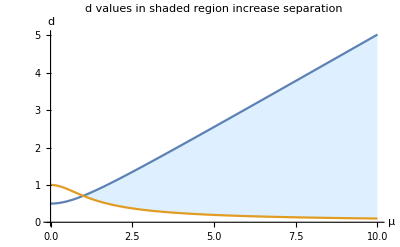

```mathematica
Plot[{1/2 √(1+μ^2),1/(√(μ^2+1))},{μ,0,10},Filling->{1->{{2},{None,LightBlue}}},AxesLabel->{"μ","d"},PlotLabel->"d values in shaded region increase separation"]
```

```mathematica
Sin[ArcCot[μ]]
```

```mathematica
1/(√(μ^2+1))
```

```mathematica
ArcCot[0]
```

π/2

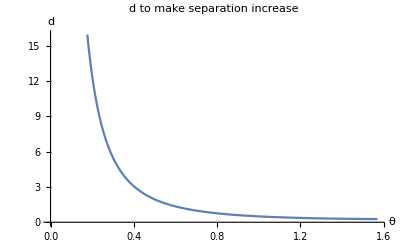

```mathematica
Plot[1/2 (1+Cot[θ]^2) Sin[ArcCot[θ]],{θ,0,π/2},AxesLabel->{"θ","d"},PlotLabel->"d to make separation increase"]
```

```mathematica
FullSimplify[Assuming[μ>0&&μ∈Reals, Sin[ArcCot[μ]]]]
```

1/(√(1+1/μ^2) μ)

```mathematica
1/(√(μ+1))
```

```mathematica
FullSimplify[(1+μ^2)1/(√(μ^2+1))]
```

√(1+μ^2)

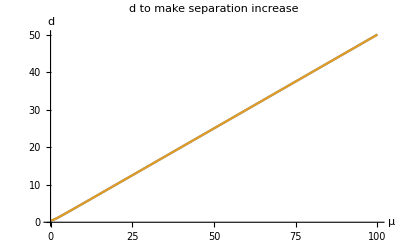

```mathematica
Plot[{1/2 (1+μ^2)1/(√(μ^2+1)),1/2 √(1+μ^2)},{μ,0,100},AxesLabel->{"μ","d"},PlotLabel->"d to make separation increase"]
```

```mathematica
Clear[d]
√((μ Sin[θ])^2+(d-Sin[θ])^2)≥ d
```

```mathematica
FullSimplify[Expand[(d-Sin[θ])^2+μ^2 Sin[θ]^2≥d^2]]
```

```mathematica
Solve[Sin[θ] (-2 d+(1+μ^2) Sin[θ])==0,d]
```

{{d→1/2 (1+μ^2) Sin[θ]}}

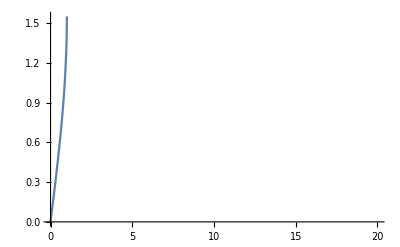

```mathematica
Plot[ArcSin[d],{d,0,20}]
```

```mathematica
Manipulate[
Module[{p1p,p2p},
p1p = {Cos[θ]-Min[Cos[θ],μ Sin[θ]],d};
p2p={Cos[θ], Sin[θ]};
If[Sin[θ]>d,θ = ArcSin[d]];
Graphics[{PointSize-> Large,
Brown,Rectangle[{-4,d},{4,d+4}],
Blue, {Opacity[0.5],Point[{0,d}]},Point[p1p],
Arrow[{{0,d},{Cos[θ],d}}],
Red, 
Arrow[{{Cos[θ],d+.02},p1p+{0,.02}}],
Arrow[{p1p,p1p+{0,-Sin[θ]}}],
 {Opacity[0.5],Point[{0,0}]},Point[p2p],
Black, Arrow[{{0,0},p2p}],
Brown, Arrow[{p1p,p2p}],Arrow[{p2p,p1p}],
Text[StringForm["   ``", Norm[ p1p-p2p]/d],1/2(p1p+p2p)]

},PlotRange->{{-.2,1.2},{-.2,d+.2}}]],
{{d,1},0,10,Appearance->"Labeled"},
{θ,0,π/2,Appearance->"Labeled"},{μ,0,10,Appearance->"Labeled"}
]
```